```mathematica
F[x_]:=1.6/π 1/(1+x^2);
p[x_]:=1/(√(2π))Exp[-x^2/2];
```

```mathematica
Integrate[F[x],{x,-5,5}]
```

1.39893

```mathematica
1/%
```

0.71483

```mathematica
Clear[a,b,data,x,y];
a=RandomReal[1,500000];
b=RandomReal[1,500000];
x=Tan[2 ArcTan[5] a-ArcTan[5]];
```

```mathematica
For[i=1;j=1,i≤500000,i++,If[b[[i]] F[x[[i]]]<p[x[[i]]],xx[j]=x[[i]];j++]]
```

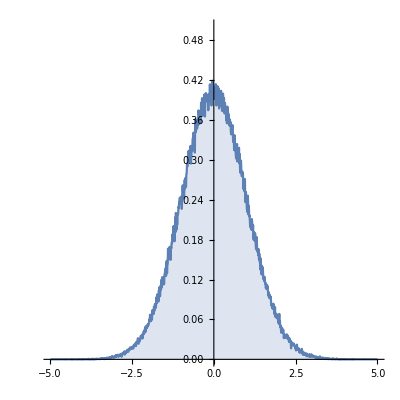

```mathematica
ca=Table[0,{i,1000}];
For[i=1,i<j,i++,ca[[Floor[100*(xx[i]+5)]+1]]++];
ca=ca/(j-1)*100;
data=Table[{-5+1/100*(i),ca[[i]]},{i,1000}];
p1=ListLinePlot[data,AspectRatio->1,Filling->Bottom,PlotRange->{0,0.5}]
```

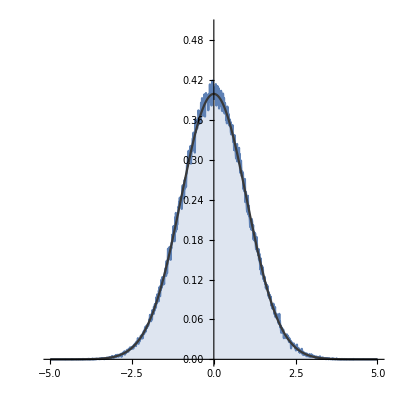

```mathematica
p2=Plot[1/(√(2Pi))Exp[-x^2/2],{x,-5,5},AspectRatio->1,ColorFunction->GrayLevel,PlotRange->{0,0.5}];
Show[p1,p2]
```

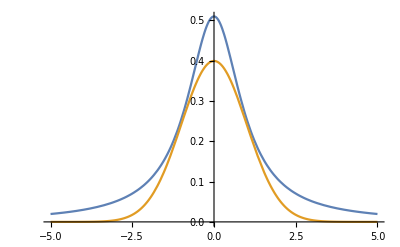

```mathematica
Plot[{F[x],p[x]},{x,-5,5}]
```

```mathematica
2ArcTan[5]
```

```mathematica
1.6*2 ArcTan[5]/Pi
```

1.39893

```mathematica
1/%
```

0.71483

```mathematica
N[%]
```

2.7468

```mathematica
Integrate[F[x],{x,-5,5}]
```

```mathematica
1.3989345337951962/Integrate[p[x],{x,-5,5}]
```

1.39894

```mathematica
1/%
```

0.714829

```mathematica
1/%
```

0.71483